100-4.9 t^2

-9.8 t

{{t→-4.51754},{t→4.51754}}

4.51754

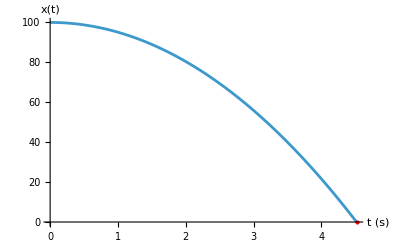

```mathematica
(*PROBLEMA 1–Queda livre*)
(*Função posição:queda livre a partir do repouso*)
x[t_]:=h-(1/2) g t^2

(*1) Derivar para achar a velocidade*)
v[t_]:=D[x[t],t]

(*2) Substituir g=9.8 e h=100*)
pos100[t_]=x[t]/. {h->100,g->9.8}
vel100[t_]=v[t]/. {h->100,g->9.8}

(*3) Determinar tempo até atingir o solo (x=0)*)
tQueda=Solve[pos100[t]==0,t]

(*Pegamos a raiz positiva*)
tempoSolo=t/. tQueda[[2]]

(*4) Gráfico da posição até o solo*)
Plot[pos100[t],{t,0,tempoSolo},PlotRange->All,AxesLabel->{"t (s)","x(t)"},Epilog->{Red,PointSize[Large],Point[{tempoSolo,0}]}]
```

```mathematica
(*PROBLEMA 2–Pêndulo não linear*)
T[θ0_,ℓ_,g_]:=Sqrt[8 ℓ/g] Integrate[1/Sqrt[Cos[θ]-Cos[θ0]],{θ,0,θ0},Assumptions->0<θ0<π]

(*Teste limite θ0 pequeno->2π Sqrt[ℓ/g]*)
FullSimplify[T[θ0,ℓ,g],{θ0->0,ℓ>0,g>0}]

(*Valor numérico para θ0=45°,ℓ=1,g=9.8*)
Tnum=N[T[Pi/4,1,9.8]]
Tsmall=2 π Sqrt[1/9.8]
Tnum/Tsmall (*razão entre período real e aproximado*)

(*Equação de movimento:θ''[t]+(g/ℓ) Sin[θ[t]]=0*)
solPend=NDSolve[{θ''[t]+(9.8/1) Sin[θ[t]]==0,θ[0]==Pi/4,θ'[0]==0},θ,{t,0,10 Tnum}];

(*Solução aproximada (harmônica) para comparação*)
θapprox[t_]:=(Pi/4) Cos[Sqrt[9.8/1] t]

(*Gráfico θ(t) exato e aproximado*)
Plot[{Evaluate[θ[t]/. solPend[[1]]],θapprox[t]},{t,0,10 Tnum},
```

(4 EllipticF[θ0/2,Csc[θ0/2]^2])/(√((g Sin[θ0/2]^2)/ℓ))

2.08732

2.00709

1.03997

```mathematica
(*PROBLEMA 3–Lançamento vertical*)


(*Função posição:lançamento para cima*)
x3[t_]:=h0+v0 t-(1/2) g t^2

(*1) Derivar para obter velocidade*)
v3[t_]:=D[x3[t],t]

(*2) Substituir h0=0,v0=20,g=9.8*)
posLanc[t_]=x3[t]/. {h0->0,v0->20,g->9.8}
velLanc[t_]=v3[t]/. {h0->0,v0->20,g->9.8}

(*3) Instante em que a velocidade zera (ponto mais alto)*)
tPico=Solve[velLanc[t]==0,t]
tempoPico=t/. tPico[[1]]

(*4) Altura máxima atingida*)
alturaMax=posLanc[tempoPico]

(*5) Tempo total de voo:resolver x(t)=0*)
tChao=Solve[posLanc[t]==0,t]
tempoTotal=t/. tChao[[2]]
```

20 t-4.9 t^2

20-9.8 t

{{t→2.04082}}

2.04082

20.4082